81.0778

3062.94

16706.9

509.427

19245.

104973.

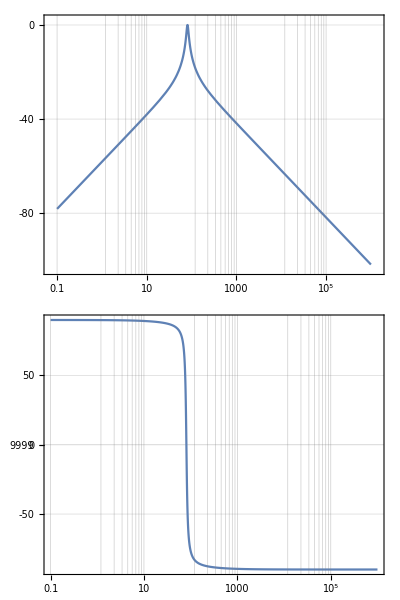

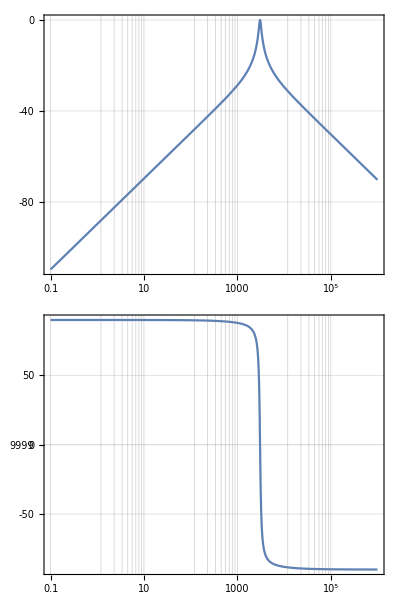

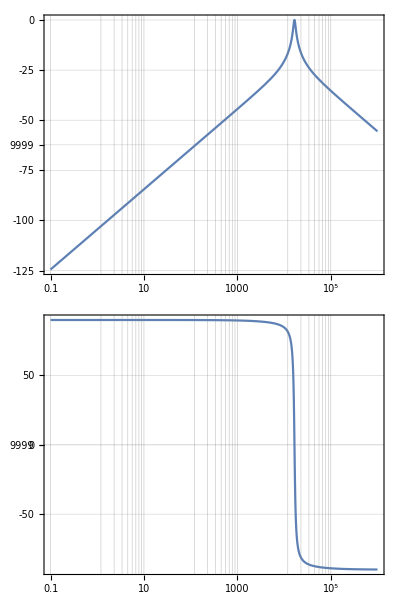

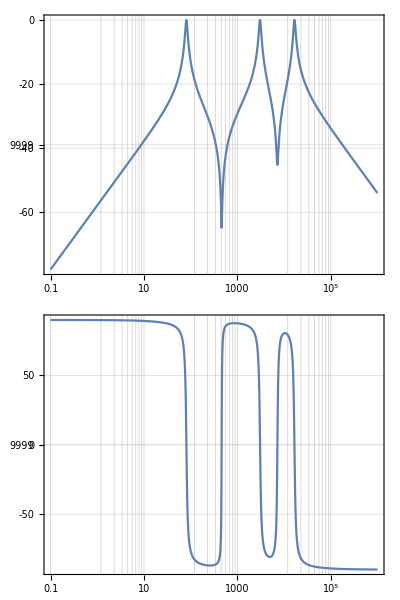

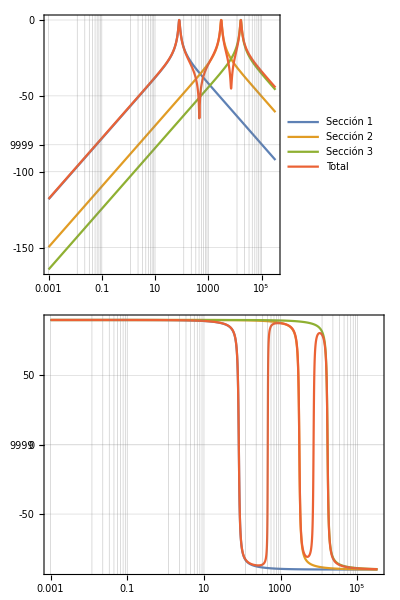

```mathematica
(*Definir parámetros*)
f01=81.0778(*Frecuencia central de la primera sección en Hz*)
f02=3062.9383(*Frecuencia central de la segunda sección en Hz*)
f03=16706.9362(*Frecuencia central de la tercera sección en Hz*)
ω01=2*Pi*f01(*Frecuencia angular de la primera sección en rad/s*)
ω02=2*Pi*f02(*Frecuencia angular de la segunda sección en rad/s*)
ω03=2*Pi*f03(*Frecuencia angular de la tercera sección en rad/s*)
Q=10;(*Factor de calidad*)
H0=1;(*Ganancia unitaria para simplificación*)

(*Funciones de transferencia individuales*)
Hs1=H0*(f01/Q)*s/(s^2+(f01/Q)*s+f01^2);
Hs2=H0*(f02/Q)*s/(s^2+(f02/Q)*s+f02^2);
Hs3=H0*(f03/Q)*s/(s^2+(f03/Q)*s+f03^2);

(*Crear modelos de función de transferencia en Mathematica*)
Hs1Model=TransferFunctionModel[Hs1,s];
BodePlot[Hs1Model,{0.1,1000000},GridLines->Automatic]
Hs2Model=TransferFunctionModel[Hs2,s];
BodePlot[Hs2Model,{0.1,1000000},GridLines->Automatic]
Hs3Model=TransferFunctionModel[Hs3,s];
BodePlot[Hs3Model,{0.1,1000000},GridLines->Automatic]

(*Suma de las funciones de transferencia*)
HsTotal=Hs1+Hs2+Hs3;
HsTotalModel=TransferFunctionModel[HsTotal,s];
BodePlot[HsTotalModel,{0.1,1000000},GridLines->Automatic]

(*Generar gráficas de Bode individuales y total*)
BodePlot[{Hs1Model,Hs2Model,Hs3Model,HsTotalModel},s,PlotLegends->{"Sección 1","Sección 2","Sección 3","Total"},GridLines->Automatic]
```